# Constrained fields

## Without known power spectrum

```mathematica
Module[{n=0,m=0},
ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]
]
```

BesselJ[0,k q]/(2 π)

```mathematica
Module[{n=1,m=0},
ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]
]
Module[{n=0,m=1},
ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]
]
```

(BesselJ[1,k q] Cos[θ])/(2 π)

(BesselJ[1,k q] Sin[θ])/(2 π)

```mathematica
Module[{n=2,m=0},
FullSimplify[ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]]
]
Module[{n=1,m=1},
FullSimplify[ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]]
]
Module[{n=0,m=2},
FullSimplify[ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]]
]
```

(-k q BesselJ[0,k q] Cos[θ]^2+BesselJ[1,k q] Cos[2 θ])/(2 k π q)

(BesselJ[2,k q] Cos[θ] Sin[θ])/(2 π)

-((BesselJ[1,k q] Cos[2 θ])/(k q)+BesselJ[0,k q] Sin[θ]^2)/(2 π)

```mathematica
Module[{n=3,m=0},
FullSimplify[ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]]
]
Module[{n=2,m=1},
FullSimplify[ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]]
]
Module[{n=1,m=2},
FullSimplify[ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]]
]
Module[{n=0,m=3},
FullSimplify[ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]]
]
```

(-k q BesselJ[1,k q] Cos[θ]^3+BesselJ[2,k q] Cos[3 θ])/(2 k π q)

-((BesselJ[1,k q] Cos[θ]^2-(BesselJ[2,k q] (1+2 Cos[2 θ]))/(k q)) Sin[θ])/(2 π)

-(Cos[θ] ((BesselJ[2,k q] (-1+2 Cos[2 θ]))/(k q)+BesselJ[1,k q] Sin[θ]^2))/(2 π)

-(k q BesselJ[1,k q] Sin[θ]^3+BesselJ[2,k q] Sin[3 θ])/(2 k π q)

```mathematica
Module[{n=4,m=0},
FullSimplify[ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]]
]
Module[{n=3,m=1},
FullSimplify[ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]]
]
Module[{n=2,m=2},
FullSimplify[ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]]
]
Module[{n=1,m=3},
FullSimplify[ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]]
]
Module[{n=0,m=4},
FullSimplify[ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}]]
]
```

1/(16 k^3 π q^3)(k q BesselJ[0,k q] (k^2 q^2 (3+4 Cos[2 θ])+(-24+k^2 q^2) Cos[4 θ])-8 BesselJ[1,k q] (-6 Cos[4 θ]+k^2 q^2 (Cos[2 θ]+Cos[4 θ])))

(-π BesselJ[2,k q] Cos[θ] Sin[θ]+(π (k q (-24+k^2 q^2) BesselJ[0,k q]-8 (-6+k^2 q^2) BesselJ[1,k q]) Sin[4 θ])/(4 k^3 q^3))/(4 π^2)

(8 (-6+k^2 q^2) BesselJ[1,k q] Cos[4 θ]+BesselJ[0,k q] (k^3 q^3+k q (24-k^2 q^2) Cos[4 θ]))/(16 k^3 π q^3)

(-π BesselJ[2,k q] Cos[θ] Sin[θ]+(π (k q (24-k^2 q^2) BesselJ[0,k q]+8 (-6+k^2 q^2) BesselJ[1,k q]) Sin[4 θ])/(4 k^3 q^3))/(4 π^2)

1/(16 k^3 π q^3)(8 BesselJ[1,k q] (k^2 q^2 (Cos[2 θ]-Cos[4 θ])+6 Cos[4 θ])+k q BesselJ[0,k q] (k^2 q^2 (3-4 Cos[2 θ])+(-24+k^2 q^2) Cos[4 θ]))

## With known power spectrum

### Correlation functions

```mathematica
corr[{n1_,m1_},{n2_,m2_},τ_:τ]:=If[EvenQ[n1+n2]∧EvenQ[m1+m2],((-1)^(n1+m1)ⅈ^(n1+m1+n2+m2)Subscript[τ, 1/2(n1+m1+n2+m2)]^2)/(2π)(2Gamma[1/2(1+n1+n2)]Gamma[1/2(1+m1+m2)])/Gamma[1+1/2(n1+m1+n2+m2)],0]
p[Y_,M_]:=Exp[-1/2 Y.Inverse[M].Y]/(√((2π)^Length[M] Det[M]))
pre[M_]:=1/(√((2π)^Length[M] Det[M]))

Cov[correlations_,τ_:τ]:=Table[corr[i,j,τ],{i,correlations},{j,correlations}]
```

```mathematica
Table[corr[{i,0},{i,0}],{i,1,5}]
```

{τ_1^2/2,(3 τ_2^2)/8,(5 τ_3^2)/16,(35 τ_4^2)/128,(63 τ_5^2)/256}

```mathematica
P[k_]:=α k^-2 ⅇ^(-R^2 k^2)
```

```mathematica
moments={
Subscript[τ, 0]->√((α R)/(2 √π)),
Subscript[τ, 1]->√(1/(2π)Integrate[k^(2 1)P[k],{k,0,∞},Assumptions->R>0]),
Subscript[τ, 2]->√(1/(2π)Integrate[k^(2 2)P[k],{k,0,∞},Assumptions->R>0]),
Subscript[τ, 3]->√(1/(2π)Integrate[k^(2 3)P[k],{k,0,∞},Assumptions->R>0]),
Subscript[τ, 4]->√(1/(2π)Integrate[k^(2 4)P[k],{k,0,∞},Assumptions->R>0]),
Subscript[τ, 5]->√(1/(2π)Integrate[k^(2 5)P[k],{k,0,∞},Assumptions->R>0])};
```

```mathematica
ξ1[q_,θ_,R_,α_]=Module[{n=1,m=0},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ2[q_,θ_,R_,α_]=Module[{n=0,m=1},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
```

(ⅇ^(-q^2/(8 R^2)) q α (BesselI[0,q^2/(8 R^2)]+BesselI[1,q^2/(8 R^2)]) Cos[θ])/(8 √π R)

(ⅇ^(-q^2/(8 R^2)) q α (BesselI[0,q^2/(8 R^2)]+BesselI[1,q^2/(8 R^2)]) Sin[θ])/(8 √π R)

```mathematica
ξ11[q_,θ_,R_,α_]=Module[{n=2,m=0},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ12[q_,θ_,R_,α_]=Module[{n=1,m=1},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ22[q_,θ_,R_,α_]=Module[{n=0,m=2},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
```

-(ⅇ^(-q^2/(8 R^2)) α (BesselI[0,q^2/(8 R^2)]-BesselI[1,q^2/(8 R^2)] Cos[2 θ]))/(8 √π R)

(ⅇ^(-q^2/(8 R^2)) α BesselI[1,q^2/(8 R^2)] Cos[θ] Sin[θ])/(4 √π R)

-(ⅇ^(-q^2/(8 R^2)) α (BesselI[0,q^2/(8 R^2)]+BesselI[1,q^2/(8 R^2)] Cos[2 θ]))/(8 √π R)

```mathematica
ξ111[q_,θ_,R_,α_]=Module[{n=3,m=0},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ112[q_,θ_,R_,α_]=Module[{n=2,m=1},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ122[q_,θ_,R_,α_]=Module[{n=1,m=2},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ222[q_,θ_,R_,α_]=Module[{n=0,m=3},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
```

(ⅇ^(-q^2/(8 R^2)) α Cos[θ] (-q^2 BesselI[0,q^2/(8 R^2)] Cos[θ]^2+BesselI[1,q^2/(8 R^2)] (q^2 Cos[θ]^2+4 R^2 (-1+2 Cos[2 θ]))))/(16 √π q R^3)

(ⅇ^(-q^2/(8 R^2)) α (-q^2 BesselI[0,q^2/(8 R^2)] Cos[θ]^2+BesselI[1,q^2/(8 R^2)] (q^2 Cos[θ]^2+4 R^2 (1+2 Cos[2 θ]))) Sin[θ])/(16 √π q R^3)

(ⅇ^(-q^2/(8 R^2)) α Cos[θ] (-q^2 BesselI[0,q^2/(8 R^2)] Sin[θ]^2+BesselI[1,q^2/(8 R^2)] (4 R^2-8 R^2 Cos[2 θ]+q^2 Sin[θ]^2)))/(16 √π q R^3)

(ⅇ^(-q^2/(8 R^2)) α Sin[θ] (-q^2 BesselI[0,q^2/(8 R^2)] Sin[θ]^2+BesselI[1,q^2/(8 R^2)] (-4 R^2-8 R^2 Cos[2 θ]+q^2 Sin[θ]^2)))/(16 √π q R^3)

```mathematica
ξ1111[q_,θ_,R_,α_]=Module[{n=4,m=0},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ1112[q_,θ_,R_,α_]=Module[{n=3,m=1},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ1122[q_,θ_,R_,α_]=Module[{n=2,m=2},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ1222[q_,θ_,R_,α_]=Module[{n=1,m=3},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ2222[q_,θ_,R_,α_]=Module[{n=0,m=4},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
```

1/(256 √π q^2 R^5)ⅇ^(-q^2/(8 R^2)) α (-4 q^2 BesselI[0,q^2/(8 R^2)] Cos[θ]^2 (q^2-12 R^2+(q^2+12 R^2) Cos[2 θ])+BesselI[1,q^2/(8 R^2)] (3 q^4+4 q^2 (q^2+4 R^2) Cos[2 θ]+(q^4+16 q^2 R^2+192 R^4) Cos[4 θ]))

1/(128 √π q^2 R^5)ⅇ^(-q^2/(8 R^2)) α (-q^2 BesselI[0,q^2/(8 R^2)] (q^2+(q^2+12 R^2) Cos[2 θ])+BesselI[1,q^2/(8 R^2)] (q^4+4 q^2 R^2+(q^4+16 q^2 R^2+192 R^4) Cos[2 θ])) Sin[2 θ]

(ⅇ^(-q^2/(8 R^2)) α (q^2 BesselI[0,q^2/(8 R^2)] (-q^2+4 R^2+(q^2+12 R^2) Cos[4 θ])+BesselI[1,q^2/(8 R^2)] (q^4-(q^4+16 q^2 R^2+192 R^4) Cos[4 θ])))/(256 √π q^2 R^5)

1/(128 √π q^2 R^5)ⅇ^(-q^2/(8 R^2)) α (q^2 BesselI[0,q^2/(8 R^2)] (-q^2+(q^2+12 R^2) Cos[2 θ])+BesselI[1,q^2/(8 R^2)] (q^4+4 q^2 R^2-(q^4+16 q^2 R^2+192 R^4) Cos[2 θ])) Sin[2 θ]

1/(256 √π q^2 R^5)ⅇ^(-q^2/(8 R^2)) α (BesselI[1,q^2/(8 R^2)] (3 q^4-4 q^2 (q^2+4 R^2) Cos[2 θ]+(q^4+16 q^2 R^2+192 R^4) Cos[4 θ])+4 q^2 BesselI[0,q^2/(8 R^2)] (-q^2+12 R^2+(q^2+12 R^2) Cos[2 θ]) Sin[θ]^2)

```mathematica
ξ11111[q_,θ_,R_,α_]=Module[{n=5,m=0},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ11112[q_,θ_,R_,α_]=Module[{n=4,m=1},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ11122[q_,θ_,R_,α_]=Module[{n=3,m=2},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ11222[q_,θ_,R_,α_]=Module[{n=2,m=3},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ12222[q_,θ_,R_,α_]=Module[{n=4,m=1},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
ξ22222[q_,θ_,R_,α_]=Module[{n=0,m=5},
Integrate[P[k] k^(n+m)ⅈ^(n+m)/(2π)^2 Integrate[ⅇ^(-ⅈ k q Cos[α-θ])Cos[α]^n Sin[α]^m,{α,0,2π},Assumptions->{k>0,q>0}],{k,0,∞},Assumptions->{q>0,R>0}]
]
```

1/(64 √π q^3 R^7)ⅇ^(-q^2/(8 R^2)) α (-BesselI[0,q^2/(8 R^2)] (q^4 (q^2-6 R^2) Cos[θ]^5+4 q^4 R^2 Cos[θ]^3 (-2+3 Cos[2 θ])+12 q^2 R^4 Cos[5 θ])+BesselI[1,q^2/(8 R^2)] (q^4 (q^2-2 R^2) Cos[θ]^5+4 q^2 R^2 (q^2+4 R^2) Cos[θ]^3 (-2+3 Cos[2 θ])+12 R^4 (q^2+16 R^2) Cos[5 θ]))

1/(128 √π q^3 R^7)ⅇ^(-q^2/(8 R^2)) α (-BesselI[0,q^2/(8 R^2)] (2 q^4 (q^2-6 R^2) Cos[θ]^4 Sin[θ]+3 q^2 R^2 (q^2 Sin[3 θ]+(q^2+8 R^2) Sin[5 θ]))+BesselI[1,q^2/(8 R^2)] (2 q^4 (q^2-2 R^2) Cos[θ]^4 Sin[θ]+3 R^2 (q^2 (q^2+4 R^2) Sin[3 θ]+(q^4+12 q^2 R^2+128 R^4) Sin[5 θ])))

1/(512 √π q^3 R^7)ⅇ^(-q^2/(8 R^2)) α (BesselI[0,q^2/(8 R^2)] (4 q^4 R^2 Cos[3 θ]+12 q^2 R^2 (q^2+8 R^2) Cos[5 θ]-8 q^4 (q^2-6 R^2) Cos[θ]^3 Sin[θ]^2)+BesselI[1,q^2/(8 R^2)] (-4 q^2 R^2 (q^2+4 R^2) Cos[3 θ]-12 R^2 (q^4+12 q^2 R^2+128 R^4) Cos[5 θ]+q^4 (q^2-2 R^2) Csc[θ] Sin[2 θ]^3))

-1/(512 √π q^3 R^7)ⅇ^(-q^2/(8 R^2)) α (-q^2 BesselI[0,q^2/(8 R^2)] (-q^4+14 q^2 R^2+96 R^4+16 R^2 (q^2+12 R^2) Cos[2 θ]+(q^4+18 q^2 R^2+192 R^4) Cos[4 θ])+BesselI[1,q^2/(8 R^2)] (-q^6+10 q^4 R^2+128 q^2 R^4+1536 R^6+16 R^2 (q^4+16 q^2 R^2+192 R^4) Cos[2 θ]+(q^6+22 q^4 R^2+288 q^2 R^4+3072 R^6) Cos[4 θ])) Sin[θ]

1/(128 √π q^3 R^7)ⅇ^(-q^2/(8 R^2)) α (-BesselI[0,q^2/(8 R^2)] (2 q^4 (q^2-6 R^2) Cos[θ]^4 Sin[θ]+3 q^2 R^2 (q^2 Sin[3 θ]+(q^2+8 R^2) Sin[5 θ]))+BesselI[1,q^2/(8 R^2)] (2 q^4 (q^2-2 R^2) Cos[θ]^4 Sin[θ]+3 R^2 (q^2 (q^2+4 R^2) Sin[3 θ]+(q^4+12 q^2 R^2+128 R^4) Sin[5 θ])))

-1/(64 √π q^3 R^7)ⅇ^(-q^2/(8 R^2)) α (BesselI[0,q^2/(8 R^2)] (-4 q^4 R^2 (2+3 Cos[2 θ]) Sin[θ]^3+q^4 (q^2-6 R^2) Sin[θ]^5+12 q^2 R^4 Sin[5 θ])+BesselI[1,q^2/(8 R^2)] (4 q^2 R^2 (q^2+4 R^2) (2+3 Cos[2 θ]) Sin[θ]^3-q^4 (q^2-2 R^2) Sin[θ]^5-12 R^4 (q^2+16 R^2) Sin[5 θ]))

### A3 line

```mathematica
mean[q_,θ_,R_,ν_]=FullSimplify[
{ξ11[q,θ,R,α],ξ12[q,θ,R,α],ξ22[q,θ,R,α],ξ111[q,θ,R,α]}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0}}]].{ν,0,c2,0}/.moments
]
variance[q_,θ_,R_,ν_]=FullSimplify[
Subscript[τ, 0]^2-
{ξ11[q,θ,R,α],ξ12[q,θ,R,α],ξ22[q,θ,R,α],ξ111[q,θ,R,α]}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0}}]].{ξ11[q,θ,R,α],ξ12[q,θ,R,α],ξ22[q,θ,R,α],ξ111[q,θ,R,α]}/.moments
]
```

-2 ⅇ^(-q^2/(8 R^2)) R^2 ((c2+ν) BesselI[0,q^2/(8 R^2)]+2 (c2-ν) BesselI[1,q^2/(8 R^2)] Cos[2 θ])

1/(480 √π q^2 R)ⅇ^(-q^2/(4 R^2)) α (240 ⅇ^(q^2/(4 R^2)) q^2 R^2-16 BesselI[0,q^2/(8 R^2)]^2 (15 q^2 R^2+2 q^4 Cos[θ]^6)+32 q^2 BesselI[0,q^2/(8 R^2)] BesselI[1,q^2/(8 R^2)] Cos[θ]^4 (q^2-8 R^2+(q^2+16 R^2) Cos[2 θ])-BesselI[1,q^2/(8 R^2)]^2 (10 q^4+512 q^2 R^2+256 R^4+3 q^2 (5 q^2+32 R^2) Cos[2 θ]+6 q^2 (q^2+16 R^2) Cos[4 θ]+(q^2+16 R^2)^2 Cos[6 θ]))

```mathematica
test=D[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},{{x,y}}],{{x,y}}];
MatrixForm[Limit[Limit[test,x->0],y->0]]
```

(λ | 0
0 | c2)

```mathematica
test=D[mean[q,θ,R,α]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,x];
Limit[Limit[test,x->0],y->0]
```

0

```mathematica
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,x],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,y],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,y,y],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},y,y,y],x->0],y->0]
```

0

0

0

«1 more identical outputs»

```mathematica
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,x,x],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,x,y],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,y,y],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,y,y,y],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},y,y,y,y],x->0],y->0]
```

(3 (c2-7 λ))/(16 R^2)

0

-(3 (c2+λ))/(16 R^2)

0

(-1344 c2 R^4+192 R^4 λ)/(1024 R^6)

```mathematica
Block[{R=1,α=1,λ=1,ν=1,c2=0},
Grid[{{
ContourPlot[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},{x,-10,10},{y,-10,10},Contours->Range[-2,2/8,1/8],PlotPoints->100,WorkingPrecision->20,PlotRange->All,ImageSize->300,Axes->True,AxesOrigin->{0,0},FrameLabel->{"q_1","q_2"}],
ContourPlot[variance[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},{x,-10,10},{y,-10,10},Contours->10,PlotPoints->100,WorkingPrecision->20,PlotRange->All,ImageSize->300,Axes->True,AxesOrigin->{0,0},FrameLabel->{"q_1","q_2"}]}}]
]
```

-Graphics-

```mathematica
MatrixForm[M=Cov[{{2,0},{1,1},{0,2},{3,0}}]]
cc2[T11_]=FullSimplify[
Integrate[T22(T11-T22)Exp[-1/2{T11,0,T22,T111}.Inverse[M].{T11,0,T22,T111}],{T22,-∞,T11},{T111,-∞,∞},Assumptions->{Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0}]/Integrate[(T11-T22)Exp[-1/2{T11,0,T22,T111}.Inverse[M].{T11,0,T22,T111}],{T22,-∞,T11},{T111,-∞,∞},Assumptions->{Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0}]
,Assumptions->{Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0}]
```

((3 τ_2^2)/8 | 0 | τ_2^2/8 | 0
0 | τ_2^2/8 | 0 | 0
τ_2^2/8 | 0 | (3 τ_2^2)/8 | 0
0 | 0 | 0 | (5 τ_3^2)/16)

T11/3+τ_2^2/(-2 T11+(ⅇ^(-(2 T11^2)/(3 τ_2^2)) √(6/π) τ_2)/(-2+Erfc[(√(2/3) T11)/τ_2]))

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

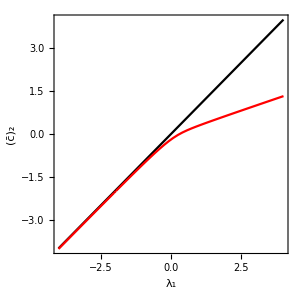

```mathematica
Block[{R=1,α=1},
Plot[Evaluate[{T11,cc2[T11]}/.moments],{T11,-4,4},WorkingPrecision->20,Frame->True,ImageSize->300,FrameLabel->{"λ_1","(c̄)_2"},AspectRatio->Automatic,PlotStyle->{Black,Red}]
]
```

```mathematica
Grid[{Block[{R=1,α=1,c2},
Table[
c2=cc2[λ]/.moments;
ContourPlot[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},{x,-10,10},{y,-10,10},(*Contours->20,*)PlotPoints->100,WorkingPrecision->20,PlotRange->All,ImageSize->300,Axes->True,AxesOrigin->{0,0},FrameLabel->{"q_1","q_2"}]
,{λ,0,1/2,1/8}]
]}]
```

-Graphics-

```mathematica
pλ1[T11_]=Module[{t=Integrate[(T11-T22)Exp[-1/2{T11,0,T22,T111}.Inverse[M].{T11,0,T22,T111}],{T22,-∞,T11},{T111,-∞,∞},Assumptions->{Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0}]},
t/Integrate[t,{T11,-∞,∞},Assumptions->{Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0}]]
```

(2 ⅇ^(-(2 T11^2)/τ_2^2) √(2/π) (ⅇ^((2 T11^2)/(3 τ_2^2)) √(6 π) T11 (1+Erf[(√(2/3) T11)/τ_2])+3 τ_2))/(9 τ_2^2)

```mathematica
Block[{R=1,α=1},
Plot[pλ1[T11]/.moments,{T11,-4,4},PlotRange->All]
]
```

-Graphics-

### A4 point

```mathematica
mean[q_,θ_,R_,ν_]=FullSimplify[
{ξ11[q,θ,R,α],ξ12[q,θ,R,α],ξ22[q,θ,R,α],ξ111[q,θ,R,α],ξ112[q,θ,R,α],ξ1111[q,θ,R,α]}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{4,0}}]].{ν,0,c3,0,0,0}/.moments
]
variance[q_,θ_,R_,ν_]=FullSimplify[
Subscript[τ, 0]^2-
{ξ11[q,θ,R,α],ξ12[q,θ,R,α],ξ22[q,θ,R,α],ξ111[q,θ,R,α],ξ112[q,θ,R,α],ξ1111[q,θ,R,α]}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{4,0}}]].{ξ11[q,θ,R,α],ξ12[q,θ,R,α],ξ22[q,θ,R,α],ξ111[q,θ,R,α],ξ112[q,θ,R,α],ξ1111[q,θ,R,α]}/.moments
]
```

1/(73 q^2)ⅇ^(-q^2/(8 R^2)) (q^2 BesselI[0,q^2/(8 R^2)] (3 c3 q^2-122 c3 R^2-21 q^2 ν-314 R^2 ν+(c3-7 ν) (4 q^2 Cos[2 θ]+(q^2+12 R^2) Cos[4 θ]))+BesselI[1,q^2/(8 R^2)] (-4 q^2 (c3 q^2+89 c3 R^2-7 q^2 ν-185 R^2 ν) Cos[2 θ]-(c3-7 ν) (3 q^4+(q^4+16 q^2 R^2+192 R^4) Cos[4 θ])))

1/(35040 √π R^3)α (17520 R^4-1/q^4 ⅇ^(-q^2/(4 R^2)) (q^4 BesselI[0,q^2/(8 R^2)]^2 (5 (35 q^4+604 q^2 R^2+4800 R^4)+20 q^2 (14 q^2+193 R^2) Cos[2 θ]+4 (35 q^4+227 q^2 R^2+1440 R^4) Cos[4 θ]+4 q^2 (10 q^2+47 R^2) Cos[6 θ]+5 (q^2+12 R^2)^2 Cos[8 θ])-2 q^2 BesselI[0,q^2/(8 R^2)] BesselI[1,q^2/(8 R^2)] (175 q^6+3600 q^4 R^2+8928 q^2 R^4+11520 R^6+4 q^2 (70 q^4+1305 q^2 R^2+8096 R^4) Cos[2 θ]+4 (35 q^6+517 q^4 R^2+1816 q^2 R^4+11520 R^6) Cos[4 θ]+4 q^2 (10 q^4+147 q^2 R^2+752 R^4) Cos[6 θ]+5 (q^2+12 R^2) (q^4+16 q^2 R^2+192 R^4) Cos[8 θ])+BesselI[1,q^2/(8 R^2)]^2 (175 q^8+4180 q^6 R^2+72736 q^4 R^4+142848 q^2 R^6+184320 R^8+4 q^2 (70 q^6+1645 q^4 R^2+9152 q^2 R^4+30720 R^6) Cos[2 θ]+4 q^4 (35 q^4+807 q^2 R^2+6832 R^4) Cos[4 θ]+4 q^2 (q^2+16 R^2) (10 q^4+87 q^2 R^2+752 R^4) Cos[6 θ]+5 (q^4+16 q^2 R^2+192 R^4)^2 Cos[8 θ])))

```mathematica
test=D[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},{{x,y}}],{{x,y}}];
MatrixForm[Limit[Limit[test,x->0],y->0]]
test=D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,x];
Limit[Limit[test,x->0],y->0]
test=D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,y];
Limit[Limit[test,x->0],y->0]
test=D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,x,x];
Limit[Limit[test,x->0],y->0]
```

(λ | 0
0 | c3)

0

0

0

```mathematica
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,x],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,y],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,y,y],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},y,y,y],x->0],y->0]
```

0

0

0

«1 more identical outputs»

```mathematica
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,x,x],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,x,y],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,y,y],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,y,y,y],x->0],y->0]
Limit[Limit[D[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},y,y,y,y],x->0],y->0]
```

0

0

-(30 c3+9 λ)/(146 R^2)

0

-(3 (65 c3-17 λ))/(146 R^2)

```mathematica
MatrixForm[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{4,0}}]]
```

((3 τ_2^2)/8 | 0 | τ_2^2/8 | 0 | 0 | -(5 τ_3^2)/16
0 | τ_2^2/8 | 0 | 0 | 0 | 0
τ_2^2/8 | 0 | (3 τ_2^2)/8 | 0 | 0 | -τ_3^2/16
0 | 0 | 0 | (5 τ_3^2)/16 | 0 | 0
0 | 0 | 0 | 0 | τ_3^2/16 | 0
-(5 τ_3^2)/16 | 0 | -τ_3^2/16 | 0 | 0 | (35 τ_4^2)/128)

```mathematica
Monitor[data=Table[
Block[{α=1,R=1,norm},
norm=NIntegrate[(λ-T22)Exp[-1/2{λ,0,T22,0,T112,-(3 T112^2)/(λ-T22)}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{4,0}}]].{λ,0,T22,0,T112,-(3 T112^2)/(λ-T22)}]/.moments,{T22,-∞,λ},{T112,-∞,∞}];
1/norm NIntegrate[T22(λ-T22)Exp[-1/2{λ,0,T22,0,T112,-(3 T112^2)/(λ-T22)}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{4,0}}]].{λ,0,T22,0,T112,-(3 T112^2)/(λ-T22)}]/.moments,{T22,-∞,λ},{T112,-∞,∞}]
]
,{λ,-4,4,0.05}];,λ]
```

```mathematica
cc3=ListInterpolation[data,{-4,4}];
```

```mathematica
Show[
Plot[T11,{T11,-4,4},PlotStyle->Black],
ListLinePlot[data,DataRange->{-4,4},PlotStyle->Red],
Frame->True,ImageSize->300,FrameLabel->{"λ_1","(c̄)_3"},AspectRatio->Automatic
]
```

-Graphics-

```mathematica
Grid[{Block[{R=1,α=1,c3},
Table[
c3=cc3[λ];
ContourPlot[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},{x,-10,10},{y,-10,10},PlotPoints->100,WorkingPrecision->20,PlotRange->All,ImageSize->300,Axes->True,AxesOrigin->{0,0},FrameLabel->{"q_1","q_2"}]
,{λ,0,1/2,1/8}]
]}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{R=1,α=1},
ContourPlot[variance[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},{x,-10,10},{y,-10,10},Contours->10,PlotPoints->100,WorkingPrecision->20,PlotRange->All,ImageSize->300,Axes->True,AxesOrigin->{0,0},FrameLabel->{"q_1","q_2"}]
]
```

-Graphics-

### D_4 point

```mathematica
mean[q_,θ_,R_,ν_]=FullSimplify[
{ξ11[q,θ,R,α],ξ12[q,θ,R,α],ξ22[q,θ,R,α],ξ111[q,θ,R,α],ξ112[q,θ,R,α],ξ122[q,θ,R,α],ξ222[q,θ,R,α]}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}}]].{ν,0,ν,0,c112,c122,c222}/.moments
]
variance[q_,θ_,R_,ν_]=FullSimplify[
Subscript[τ, 0]^2-
{ξ11[q,θ,R,α],ξ12[q,θ,R,α],ξ22[q,θ,R,α],ξ111[q,θ,R,α],ξ112[q,θ,R,α],ξ122[q,θ,R,α],ξ222[q,θ,R,α]}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}}]].{ξ11[q,θ,R,α],ξ12[q,θ,R,α],ξ22[q,θ,R,α],ξ111[q,θ,R,α],ξ112[q,θ,R,α],ξ122[q,θ,R,α],ξ222[q,θ,R,α]}/.moments
]
```

-1/(3 q)2 ⅇ^(-q^2/(8 R^2)) R^2 (-BesselI[1,q^2/(8 R^2)] (c122 q^2 Cos[θ]-3 c122 (q^2+16 R^2) Cos[3 θ]+(c112+c222) q^2 Sin[θ]+(3 c112-c222) (q^2+16 R^2) Sin[3 θ])+q BesselI[0,q^2/(8 R^2)] (6 ν+q (c122 Cos[θ]-3 c122 Cos[3 θ]+(c112+c222) Sin[θ]+(3 c112-c222) Sin[3 θ])))

1/(12 √π q^2 R)ⅇ^(-q^2/(4 R^2)) α (6 ⅇ^(q^2/(4 R^2)) q^2 R^2-(q^4+6 q^2 R^2) BesselI[0,q^2/(8 R^2)]^2+2 q^2 (q^2+8 R^2) BesselI[0,q^2/(8 R^2)] BesselI[1,q^2/(8 R^2)]-(q^4+28 q^2 R^2+128 R^4) BesselI[1,q^2/(8 R^2)]^2)

```mathematica
MatrixForm[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}}]]
```

((3 τ_2^2)/8 | 0 | τ_2^2/8 | 0 | 0 | 0 | 0
0 | τ_2^2/8 | 0 | 0 | 0 | 0 | 0
τ_2^2/8 | 0 | (3 τ_2^2)/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | (5 τ_3^2)/16 | 0 | τ_3^2/16 | 0
0 | 0 | 0 | 0 | τ_3^2/16 | 0 | τ_3^2/16
0 | 0 | 0 | τ_3^2/16 | 0 | τ_3^2/16 | 0
0 | 0 | 0 | 0 | τ_3^2/16 | 0 | (5 τ_3^2)/16)

```mathematica
Block[{R=1,α=1,λ=1},
NIntegrate[
{T111,T112,T122,T222}HeavisideTheta[(T111-T122)T122-(T222-T112)T112]Exp[-1/2{λ,0,λ,T111,T112,T122,T222}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}}]].{λ,0,λ,T111,T112,T122,T222}]/.moments,{T112,-∞,∞},{T122,-∞,∞},{T222,-∞,∞},{T111,-∞,∞}]/NIntegrate[
HeavisideTheta[(T111-T122)T122-(T222-T112)T112]Exp[-1/2{λ,0,λ,T111,T112,T122,T222}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}}]].{λ,0,λ,T111,T112,T122,T222}]/.moments,{T112,-∞,∞},{T122,-∞,∞},{T222,-∞,∞},{T111,-∞,∞}]]

Block[{R=1,α=1,λ=1},
NIntegrate[
{T111,T112,T122,T222}HeavisideTheta[-(T111-T122)T122+(T222-T112)T112]Exp[-1/2{λ,0,λ,T111,T112,T122,T222}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}}]].{λ,0,λ,T111,T112,T122,T222}]/.moments,{T112,-∞,∞},{T122,-∞,∞},{T222,-∞,∞},{T111,-∞,∞}]/NIntegrate[
HeavisideTheta[-(T111-T122)T122+(T222-T112)T112]Exp[-1/2{λ,0,λ,T111,T112,T122,T222}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}}]].{λ,0,λ,T111,T112,T122,T222}]/.moments,{T112,-∞,∞},{T122,-∞,∞},{T222,-∞,∞},{T111,-∞,∞}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.64577×10^-22 and 3.90991×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.64041×10^-22 and 1.04821×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.38419×10^-22 and 4.53142×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-2.36611×10^-7,-3.7961×10^-7,-6.30313×10^-7,1.16299×10^-17}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.2326×10^-32 and 4.75663×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.68632×10^-22 and 4.28791×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.36033×10^-23 and 1.77772×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-1.77457×10^-17,1.25057×10^-6,-1.95847×10^-8,2.83855×10^-6}

```mathematica
Block[{R=1,α=1,λ=1},
NIntegrate[
{T111,T112,T122,T222}HeavisideTheta[(T111-T122)T122-(T222-T112)T112]Exp[-1/2{λ,0,λ,T111,T112,T122,T222}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}}]].{λ,0,λ,T111,T112,T122,T222}]/.moments/.T111->0,{T112,-∞,∞},{T122,-∞,∞},{T222,-∞,∞}]/NIntegrate[
HeavisideTheta[(T111-T122)T122-(T222-T112)T112]Exp[-1/2{λ,0,λ,T111,T112,T122,T222}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}}]].{λ,0,λ,T111,T112,T122,T222}]/.moments/.T111->0,{T112,-∞,∞},{T122,-∞,∞},{T222,-∞,∞}]]

Block[{R=1,α=1,λ=1},
NIntegrate[
{T111,T112,T122,T222}HeavisideTheta[-(T111-T122)T122+(T222-T112)T112]Exp[-1/2{λ,0,λ,T111,T112,T122,T222}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}}]].{λ,0,λ,T111,T112,T122,T222}]/.moments/.T111->0,{T112,-∞,∞},{T122,-∞,∞},{T222,-∞,∞}]/NIntegrate[
HeavisideTheta[-(T111-T122)T122+(T222-T112)T112]Exp[-1/2{λ,0,λ,T111,T112,T122,T222}.Inverse[Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}}]].{λ,0,λ,T111,T112,T122,T222}]/.moments/.T111->0,{T112,-∞,∞},{T122,-∞,∞},{T222,-∞,∞}]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.39087×10^-22 and 3.6106×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.35155×10^-17 and 4.044×10^-19 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand ⅇ^(1/2 (-32 √π-(320 √π T122^2)/3-T112 (320/3 Power[«2»] T112-64/3 Power[«2»] T222)-T222 (-64/3 Power[«2»] T112+64/3 Power[«2»] T222))) T122 HeavisideTheta[-T122^2-T112 (-T112+T222)] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.70143×10^-21 and 1.03768×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{0.,1.41415×10^-7,0.,-1.00636×10^-6}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.84889×10^-32 and 2.71069×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2706×10^-16 and 6.×10^-19 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand ⅇ^(1/2 (-32 √π-(320 √π T122^2)/3-T112 (320/3 Power[«2»] T112-64/3 Power[«2»] T222)-T222 (-64/3 Power[«2»] T112+64/3 Power[«2»] T222))) T122 HeavisideTheta[T122^2+T112 (-T112+T222)] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.66522×10^-23 and 1.87314×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{0.,4.46799×10^-18,0.,-1.12739×10^-8}

```mathematica
test=D[D[mean[q,θ,R,ν]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},{{x,y}}],{{x,y}}];
MatrixForm[Limit[Limit[test,x->0],y->0]]

test=D[mean[q,θ,R,ν]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},x,x,x];
Limit[Limit[test,x->0],y->0]
```

(ν | 0
0 | ν)

0

```mathematica
Block[{R=1,α=1,λ=1},
Grid[{{
ContourPlot[mean[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2),c112->0,c122->0,c222->0},{x,-10,10},{y,-10,10},PlotPoints->100,WorkingPrecision->20,PlotRange->All,ImageSize->300,Axes->True,AxesOrigin->{0,0},FrameLabel->{"q_1","q_2"}],
ContourPlot[variance[q,θ,R,λ]/.{θ->ArcTan[x,y],q->√(x^2+y^2)},{x,-10,10},{y,-10,10},Contours->10,PlotPoints->100,WorkingPrecision->20,PlotRange->All,ImageSize->300,Axes->True,AxesOrigin->{0,0},FrameLabel->{"q_1","q_2"}]}}]
]
```

-Graphics- | -Graphics-